## Random XX chain: entanglement entropy

```mathematica
L=128;
ll=64;
shift=32;
(*nsample=5;
data={};
Monitor[For[n=1,n≤nsample,n++,
*)JJ=Table[RandomReal[],{i,1,L-1}];
JJ={0.185082,0.931541,0.947731,0.484749,0.320536,0.154427,0.698863,0.119951,0.485176,0.632738,0.818227,0.683026,0.498561,0.586797,0.719754,0.258498,0.546207,0.407308,0.176985,0.969632,0.297018,0.287869,0.116193,0.181727,0.49429,0.565765,0.221835,0.767491,0.577308,0.167823,0.367471,0.468674,0.654266,0.79309,0.663062,0.61303,0.990852,0.119485,0.148565,0.852281,0.509526,0.21727,0.993266,0.315297,0.258733,0.809175,0.353675,0.467842,0.274173,0.7982,0.814138,0.94809,0.822885,0.515139,0.220998,0.746631,0.431538,0.888304,0.941193,0.503012,0.702042,0.706542,0.481022,0.960314,0.426023,0.322874,0.76193,0.932629,0.711217,0.517431,0.884472,0.553634,0.573642,0.393933,0.926547,0.00554442,0.728499,0.355754,0.212933,0.362027,0.8783,0.363326,0.503207,0.767488,0.914476,0.826368,0.411746,0.630843,0.341912,0.381693,0.96246,0.647014,0.957846,0.803452,0.229386,0.879202,0.592496,0.786172,0.532144,0.968291,0.574954,0.476843,0.421138,0.59898,0.106573,0.368608,0.215806,0.807211,0.798221,0.554539,0.895146,0.92914,0.977633,0.917719,0.0400112,0.732822,0.896374,0.837831,0.536454,0.321319,0.397254,0.277439,0.936248,0.463743,0.852289,0.212767,0.000123584};
AppendTo[JJ,0];T=Table[(KroneckerDelta[i,j-1] JJ⟦j-1⟧)/2.+(KroneckerDelta[i,j+1] JJ⟦j⟧)/2.,{i,1,L},{j,1,L}];Spect=Eigensystem[T];ind=Table[i,{i,1,L}];eigval=Spect⟦1⟧;ind=Select[ind,eigval⟦#1⟧<0&];eigvec=Table[Spect⟦2,ind⟦k⟧⟧,{k,1,Length[ind]}];Corr[x_,y_]:=Total[Table[eigvec⟦q,x⟧ eigvec⟦q,y⟧,{q,1,Length[eigvec]}]];ent={};For[k=1,k≤L/4,k++,shift=1/2 (L-2 k);ll=2 k;cmat=Table[Corr[shift+x,shift+y],{x,1,ll},{y,1,ll}];eeig=Eigenvalues[cmat];Ent=∑_(i=1)^Length[eeig] If[Abs[eeig⟦i⟧]>0&&Abs[eeig⟦i⟧]<1,(1-eeig⟦i⟧) (-Log[1-eeig⟦i⟧])-eeig⟦i⟧ Log[eeig⟦i⟧],0];AppendTo[ent,{2k,Ent}];];(*AppendTo[data,ent];];,{n}]*)
```

```mathematica
ex=Import["/u/he/valba/Github/negatitivy/ran_negativity/mathematica/re"] ;
```

```mathematica
ex[[3]]
```

{{1.383628902159025,1.81055,1.43248,1.39516,1.62983,1.42628,2.1353, 1.9119885950487108 + 1.2599858674912698*^-15*I,1.57245,2.06775, 1.7872774326297372 + 1.0931349472878151*^-15*I, 1.8953178403155464 + 6.270384076621184*^-16*I, 1.5083824124404257 + 1.0328330607015858*^-15*I, 2.3908333110367845 + 2.2602515226747766*^-15*I, 1.6209414088484106 + 8.380312721548843*^-16*I, 2.0796521755145303 + 3.3801724110061083*^-15*I, 2.3465777886053774 + 6.294449863093254*^-15*I, 2.0830824875998535 + 3.4699650337039792*^-15*I, 2.6915301511084624 + 4.385245803933934*^-15*I, 1.4907855842373379 + 6.094734018503764*^-15*I, 2.744899475597132 + 5.591985963694587*^-15*I, 2.3544245124874816 + 4.2675088586950095*^-15*I, 2.9118718558914036 + 4.263126614193246*^-15*I, 2.8706538777475843 + 4.431545177104931*^-15*I, 2.914714925111556 + 6.7334731402088055*^-15*I, 2.4456069508659812 + 7.487711922975561*^-15*I, 2.0425310810482507 + 6.087491532021622*^-15*I, 2.2290157939759454 + 7.079765827709471*^-15*I, 2.550930015304841 + 8.25982165869359*^-15*I, 2.205144265321108 + 5.996650565533444*^-15*I, 1.4079009468506314 + 1.1378284051590499*^-14*I, 2.4447667325285 + 9.100254901487923*^-15*I}}

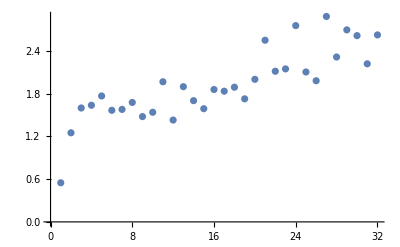

```mathematica
ent//ListPlot
```